```mathematica
SetDirectory[DirectoryName[NotebookDirectory[],1]<>"\\Mathematica Packages"]
Get["JointIBD`"];
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
```

D:\Codes\Mathematica\JointIBD_MathematicaCode\Mathematica Packages

D:\Codes\Mathematica\JointIBD_MathematicaCode\JointIBD Inference

```mathematica
filels=FileNames["Data_*.txt"]
```

{Data_L-LD.txt,Data_L-NoLD.txt,Data_S-LD.txt,Data_S-NoLD.txt}

```mathematica
isphased=True;
datafile=filels[[4]]
dataid=StringDrop[datafile,-4]
outcold="JointIBD_OutCold_"<>If[isphased,"Phased_","Unphased_"]<>datafile
```

Data_S-NoLD.txt

Data_S-NoLD

JointIBD_OutCold_Phased_Data_S-NoLD.txt

```mathematica
linethick=0.004;
plotstyle={Black,Thickness[linethick]};
```

```mathematica
$Packages
```

{ErrorBarPlots`,Toolbox`,Metropolis`,ChineseRestaurantProcess`,JointIBD`Likelihood`,JointIBD`,GetFEKernelInit`,ResourceLocator`,PacletManager`,QuantityUnits`,WebServices`,System`,Global`}

```mathematica
acf[x:{__Real},kk_Integer]:=Module[{p=Mean[x],l=Length[x]},Table[Sum[(x⟦t⟧-p) (x⟦t-k⟧-p),{t,k+1,l}]/(l-k)/Sum[((x⟦t⟧-p)^2)/l,{t,1,l}],{k,0,kk}]];
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
Block[{temp,r},
popunit=10^(-6.);
temp=ReadList[StringReplace[datafile,"Data"->"TrueValues"]];
{nbp,nsq,trueepsilon}=temp[[1]];
{errind,ibdls}=Split[Rest[temp],Depth[#1[[2]]]==Depth[#2[[2]]]&];
ls=SplitBy[ibdls,Last];
ls=ls[[All,1]];
{trueibdloc,trueibd}=Transpose[ls];
ysnp=Rest[ReadList[datafile]];
trueaf=ysnp[[All,-1]];
];
```

```mathematica
Print["Alleles counts: ",Tally[Flatten[errind[[All,2]]]]]
Print["realized error rate: ",N[Mean[Flatten[errind[[All,2]]]]]];
Print["realized #visisble IBD transtions: ",(Length[trueibd]-1)," over length of ",nbp/10^6,"Mbp"];
ls=(IBDTransitionType2[#]&/@Partition[trueibd,2,1])[[All,1]];
Print["transtion types: ",ls];
Print["tally: ",Tally[ls]];
```

Alleles counts: {{0,3388},{1,12}}

realized error rate: 0.00352941

realized #visisble IBD transtions: 18 over length of 1Mbp

transtion types: {1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1}

tally: {{1,16},{2,2}}

```mathematica
Dimensions[#]&/@{ysnp,trueibd,errind}
```

{{85,3},{19},{85,2}}

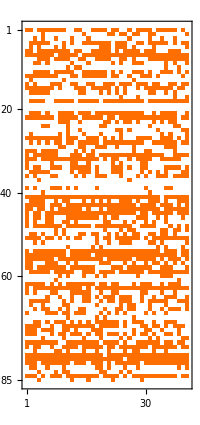

```mathematica
MatrixPlot[ysnp[[All,2]]]
```

```mathematica
(*The prior distribution of theta is Gamma[shape, scale], truncated to be in the range [min, max]];
pritheta={shape,scale,min,max};*)
pritheta={2,2 nsq,0,Infinity};
(*The prior distribution of rho is Gamma[shape, scale], truncated to be in the range [min, max]];
prirho={shape,scale,min,max};*)
prirho={2,10^(-4),0,Infinity};
(*The prior distribution of epsilon is Beta[alpha,beta], truncated to be in the range [min, max]];
prieps={alpha,beta,min,max};*)
prieps={1,1,0,1};
(*maxcpden × chromsome length in Mbp = max number of IBD change-points*)
maxcpden=Infinity;
If[StringCount[datafile,"-LD"]==1,
maxcpden=20;
pritheta[[3]]=nsq;
];
```

```mathematica
{prithetashape,prithetascale,prithetamin,prithetamax}=pritheta;
{prirhoshape,prirhoscale,prirhomin,prirhomax}=prirho;
{priepsalpha,priepsbeta,priepsmin,priepsmax}=prieps;
thetadist=TruncatedDistribution[{prithetamin,prithetamax},GammaDistribution[prithetashape,prithetascale]];
rhodist=TruncatedDistribution[{prirhomin,prirhomax}/popunit,GammaDistribution[prirhoshape,prirhoscale/popunit]]
epsdist=TruncatedDistribution[{priepsmin,priepsmax},BetaDistribution[priepsalpha,priepsbeta]];
```

TruncatedDistribution[{0.,∞},GammaDistribution[2,100.]]

```mathematica
(*****************************************************************************************************************)
```

```mathematica
rescold0=Drop[Drop[ReadList[outcold],-1],1];//Timing
rescold0[[All,All,3,3]]/=popunit;
Dimensions[rescold0]
```

{1.65361,Null}

{231,2,6}

```mathematica
(*****************************************************************************************************************)
```

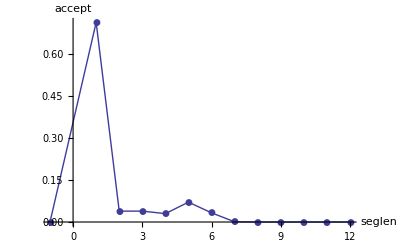
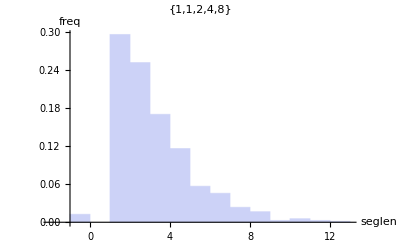

```mathematica
If[1==1,
ls=rescold0[[;;;;1,All,5,6]];
Dimensions[ls];
temp=Flatten[ls[[All,1]],1];
temp2=SplitBy[SortBy[temp,First],First];
temp2=Mean[#]&/@temp2;
{ListPlot[temp2,PlotMarkers->Automatic,Joined->True,PlotRange->All,AxesLabel->{"seglen","accept"}],Histogram[temp[[All,1]],Automatic,"PDF",AxesLabel->{"seglen","freq"},PlotLabel->Quantile[temp[[All,1]],{0.025,0.25,0.5,0.75,0.975}]]}
]
```

```mathematica
ls=Select[temp,0<=First[#]≤12&];
Mean[ls[[All,-1]]]
```

0.238424

```mathematica
(*****************************************************************************************************************)
```

```mathematica
rescoldncp=Map[Length,rescold0[[All,All,4]],{2}];//Timing
Dimensions[rescoldncp]
```

{0.,Null}

{231,2}

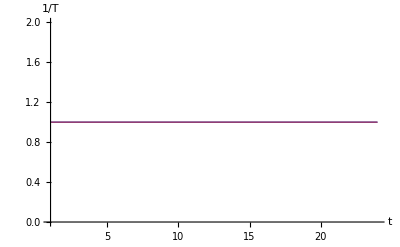
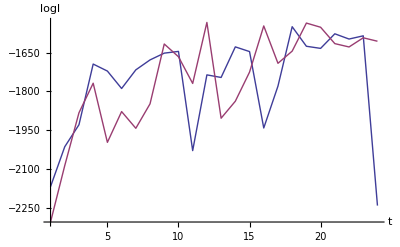
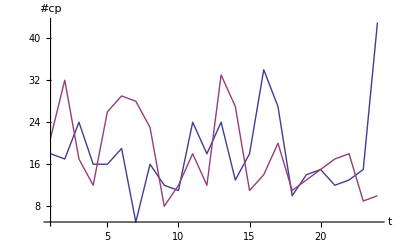
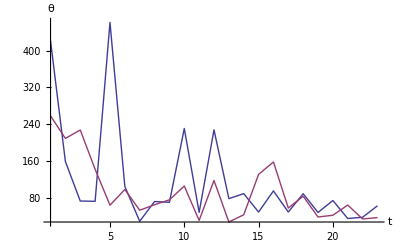
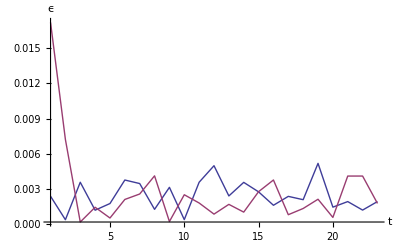
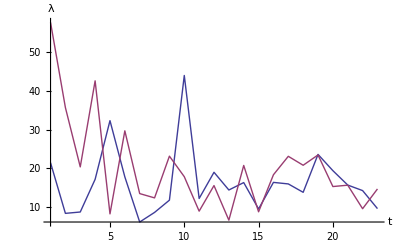

```mathematica
lab={"θ","ϵ","λ"};
{{ListLinePlot[Transpose[rescold0[[;;;;10,All,1]]],PlotRange->All,AxesLabel->{"t","1/T"}],
ListLinePlot[Transpose[rescold0[[;;;;10,All,2]]],PlotRange->All,AxesLabel->{"t","logl"}],ListLinePlot[Transpose[rescoldncp[[;;;;10]]],PlotRange->All,AxesLabel->{"t","#cp"}]},
{Table[ListLinePlot[Transpose[rescold0[[10;;;;10,All,3,i]]],PlotRange->All,AxesLabel->{"t",lab[[i]]}],{i,3}]}}
```

{24,2,3,2}

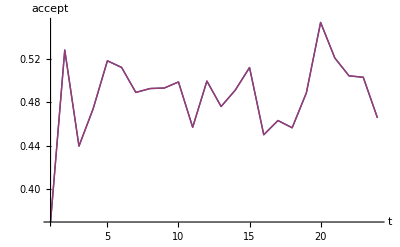
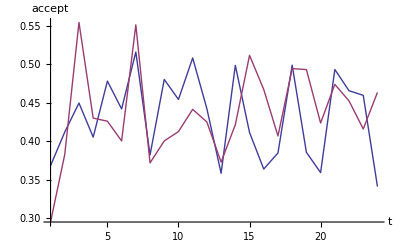
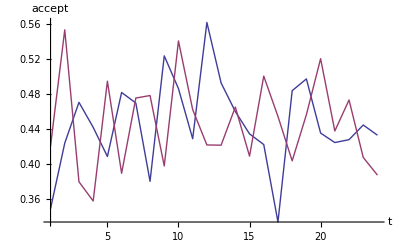
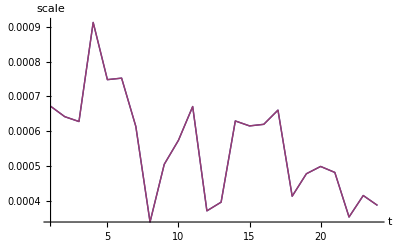
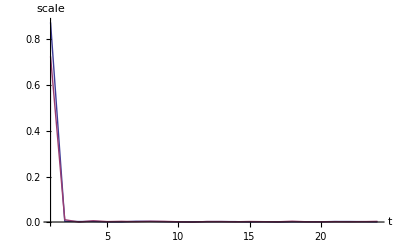
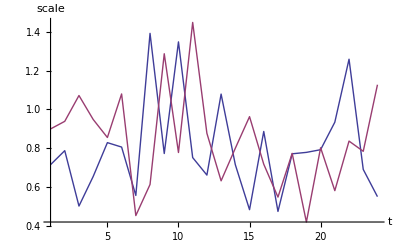

```mathematica
ls=rescold0[[;;;;10,All,5,;;3]];
Dimensions[ls]
Table[ListLinePlot[Transpose[ls[[All,All,j,i]]],PlotRange->All,AxesLabel->{"t",If[i==1,"accept","scale"]}],{i,2},{j,3}]
```

{231,2,7}

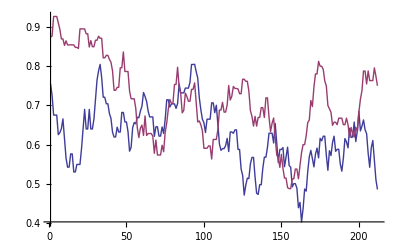
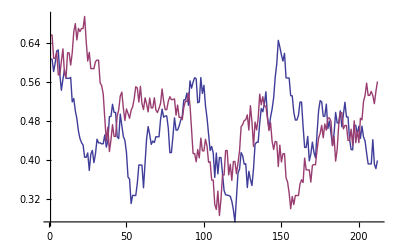
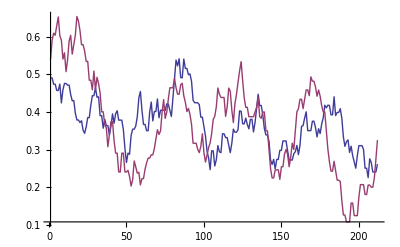
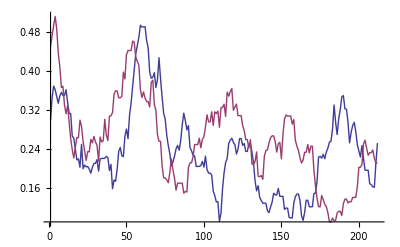
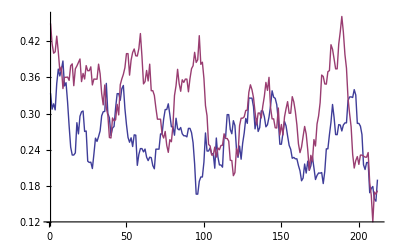
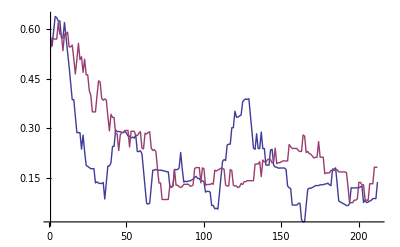
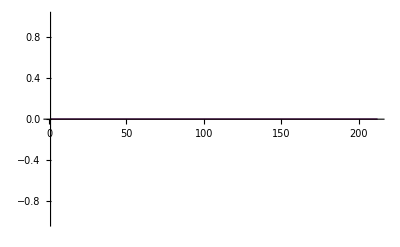

```mathematica
ls=rescold0[[;;;;1,All,5,5]];
Dimensions[ls]
Table[ListLinePlot[Transpose[MovingAverage[ls[[All,All,i]],20]],PlotRange->All],{i,Dimensions[ls][[3]]}]
```

{2,231}

{2,231}

{2,231}

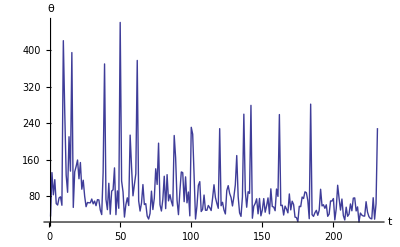
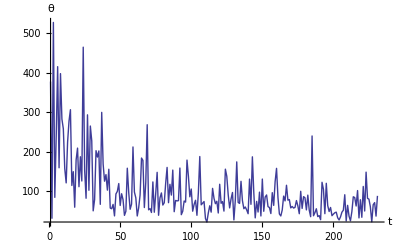
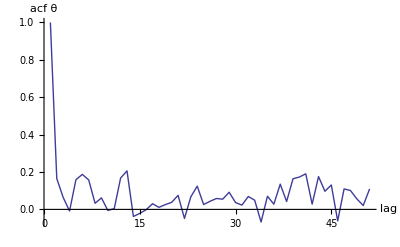
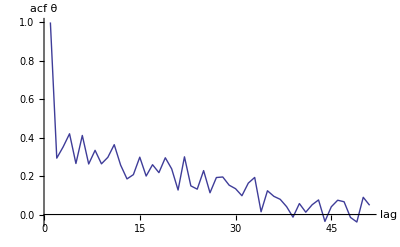
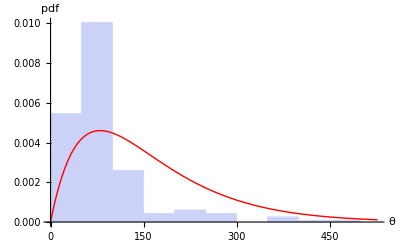
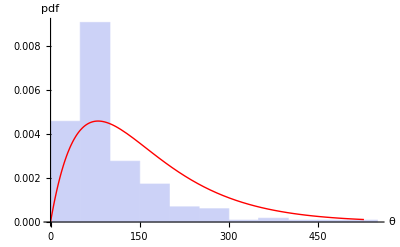
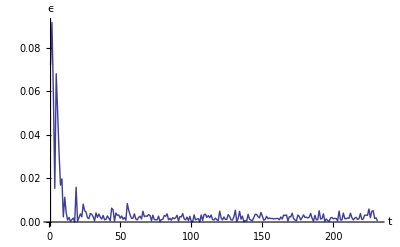
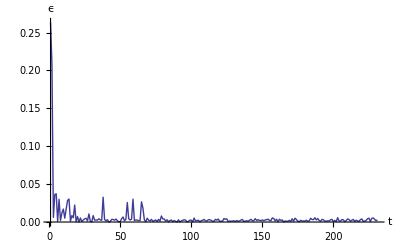

```mathematica
nchain=Dimensions[rescold0][[2]];
lab={"θ","ϵ","ρ"};
dist={thetadist,epsdist,rhodist};
gg=Table[
ls=Transpose[rescold0[[All,All,3,i]]];
Print[Dimensions[ls]];
pri=Plot[PDF[dist[[i]],x],{x,0,Max[ls]},PlotStyle->{Red,Thick},PlotRange->All];
ts=ListLinePlot[#,PlotRange->All,AxesLabel->{"t",lab[[i]]}]&/@ls;
af=ListLinePlot[acf[N[Take[#,-Min[500,Dimensions[ls][[2]]-1]]],50],AxesOrigin->{0,0},AxesLabel->{"lag","acf "<>lab[[i]]},PlotRange->All]&/@ls;
his=Histogram[#,Automatic,"PDF",AxesLabel->{lab[[i]],"pdf"}]&/@ls;
hisp=Show[{#,pri},PlotRange->All]&/@his;
{Partition[ts,nchain/2],Partition[af,nchain/2],Partition[hisp,nchain/2]},{i,3}]
```

{0.,Null}

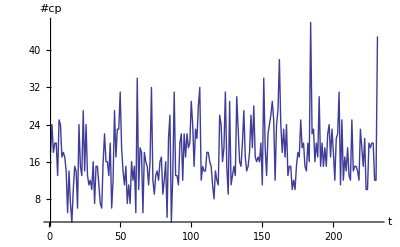
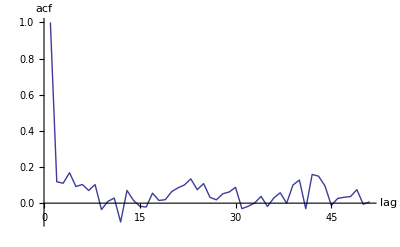
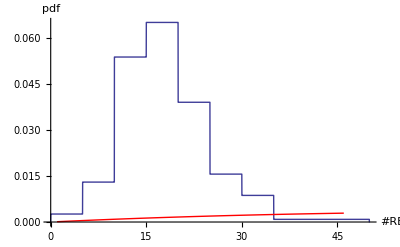
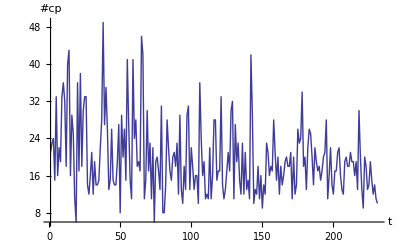
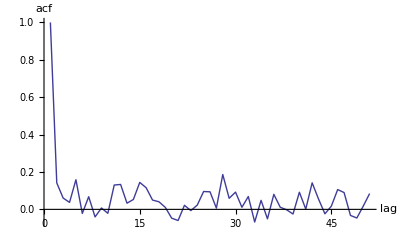
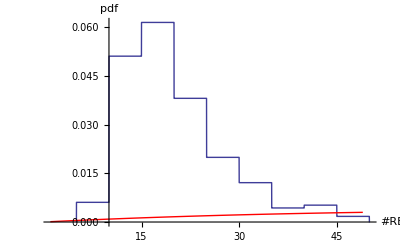

```mathematica
princpdist=NegativeBinomialDistribution[prirhoshape,prirhoscale^(-1)/(prirhoscale^(-1)+nbp)];
Clear[x]
fun=PDF[princpdist,x-1];
rescoldncp=Map[Length,rescold0[[All,All,4]],{2}];//Timing
Table[
ls=rescoldncp[[All,i]];
ts=ListLinePlot[ls,PlotRange->All,AxesLabel->{"t","#cp"}];
af=ListLinePlot[acf[N[ls],50],AxesOrigin->{0,0},AxesLabel->{"lag","acf"},PlotRange->All];
princp=Plot[fun,{x,1,Max[ls]},PlotStyle->{Red,Thick},PlotRange->All];
his=Show[PosteriorPDFPlot[ls,0,PlotRange->All],princp,PlotRange->All,AxesLabel->{"#RE","pdf"}];
{ts,af,his},{i,Dimensions[rescoldncp][[2]]}]
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
Dimensions[rescold0]
```

{231,2,6}

```mathematica
If[1==1,
burnin=Ceiling[1Length[rescold0]/6];
thin=1,
burnin=-2000;
thin=2;
];
rescold=rescold0[[burnin;;;;thin]];
If[1==1,
rescold=Join@@Table[rescold[[All,i]],{i,Dimensions[rescold][[2]]}],
rescold=rescold[[All,1]];
];
Dimensions[rescold]
```

{386,6}

{0.,Null}

-----------------------Start----------------------------

Geweke Convergence Diagnositics for the 2nd half chains:

Chain 1: 
 | logl | theta | epsilon | rho | #cp
Z-Score | -2.07014 | 5.09186 | -1.62407 | 0.0677045 | 0.504116
P-Value | 0.0384393 | 3.54572×10^-7 | 0.104362 | 0.946021 | 0.61418

Chain 2: 
 | logl | theta | epsilon | rho | #cp
Z-Score | -1.18058 | 0.848992 | -0.733358 | 0.252818 | 0.57338
P-Value | 0.23777 | 0.395886 | 0.46334 | 0.800409 | 0.566388

--------------------------------------------------------

Brooks, Gelman, and Rubin Convergence Diagnositics:

Potential Scale Reduction Factors for the 2nd half chains:
 | logl | theta | epsilon | rho | #cp
PSRF | 1.00432 | 0.996137 | 1.02557 | 1.00978 | 1.01456

Trace plot of PSRF:

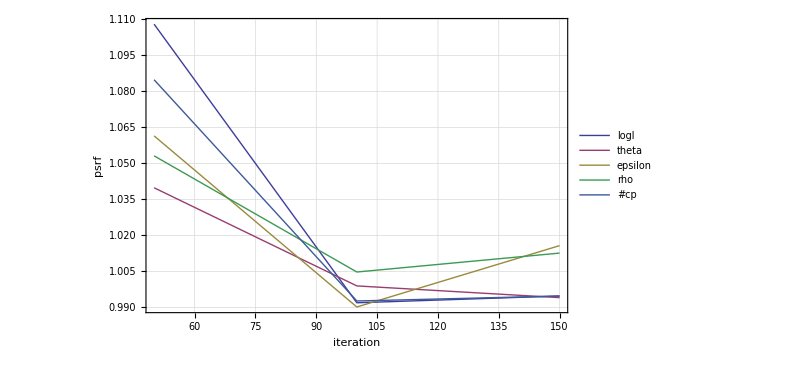

----------------------The End--------------------------

```mathematica
temp=Map[Join[{#[[2]]},#[[3]],{N[Length[#[[4]]]]}]&,rescold0,{2}];//Timing
MCMCDiagostic[temp[[burnin;;]],{"logl","theta","epsilon","rho","#cp"}]
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
Clear[listmcplot,listhisplot]
listmcplot[mc_,truevalue_,lab_,withdata_,opts___]:=Module[{dim,g1,g2},
dim=Length[lab];
g1=Table[ListPlot[mc[[All,i]],Joined->True,PlotRange->All,AxesLabel->{"×"<>ToString[thin]<>" t",lab[[i]]}],{i,dim}];
g2=Table[ListPlot[{{0,truevalue[[i]]}},PlotMarkers->{Automatic,16},PlotRange->All,PlotStyle->{Blue,Red}],{i,dim}];
If[withdata,Show[#,opts]&/@Transpose[{g1,g2}],Show[#,opts]&/@g1]
];

listhisplot[mc_,truevalue_,lab_,withdata_,ticks_,opts___]:=Module[{dim,g1,g2,g11},
dim=Length[lab];
(*g1=Table[Histogram[mc[[All,i]],Automatic,"PDF",PlotRange->All,Ticks->ticks[[i]],AxesLabel->{lab[[i]],"pdf"}],{i,dim}];*)
g1=Table[PosteriorPDFPlot[mc[[All,i]],1,PlotRange->All,Ticks->ticks[[i]],PlotStyle->{Black,Thickness[linethick]},AxesLabel->{lab[[i]],"pdf"}],{i,dim}];
g2=Table[ListPlot[{{truevalue[[i]],If[i==2,10,0]}},PlotMarkers->{Automatic,16},PlotStyle->Magenta],{i,dim}];
If[withdata,Show[#,opts]&/@Transpose[{g1,g2}],Show[#,opts]&/@g1]
];
```

```mathematica
modelid=If[StringCount[datafile,"-LD"]==1,"LD","NoLD"]
prires=ReadList["prinRE_"<>modelid<>".txt"];
```

NoLD

```mathematica
resnRE=Table[Count[Equal@@#&/@Partition[rescold[[k,4,All,2]],2,1],False],{k,Length[rescold]}];
resnRE=resnRE 10^6./nbp;
```

```mathematica
nvRE=(Length[trueibd]-1)  10^6./nbp
```

18.

```mathematica
Count[resnRE,_?(#>nvRE&)]
%/Length[resnRE]//N
Length[resnRE]
```

2

0.00518135

386

```mathematica
truehyper={truetheta,trueepsilon,truerho,None}
hyperlab={"θ","ε","λ","K"};
reshyper=Transpose[Append[Transpose[rescold[[All,3]]],resnRE]];
Dimensions[reshyper]
Mean[reshyper]//N
```

{truetheta,0.005,truerho,None}

{386,4}

{80.6589,0.00250466,18.8035,9.63731}

```mathematica
DistributionFitTest[reshyper[[All,1]],thetadist]
DistributionFitTest[reshyper[[All,2]],epsdist]
DistributionFitTest[reshyper[[All,3]],rhodist]
```

8.88178×10^-15

8.88178×10^-15

5.44009×10^-15

```mathematica
Dimensions[ls]
```

{231}

```mathematica
withdata=True;
```

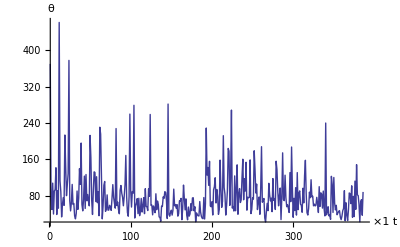
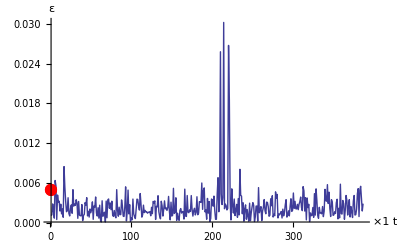
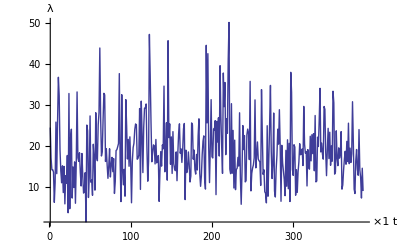
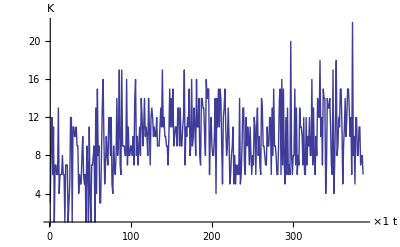

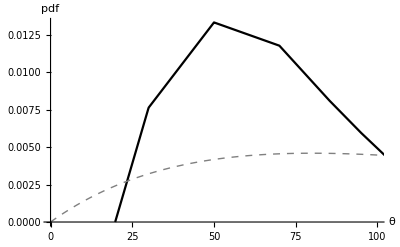
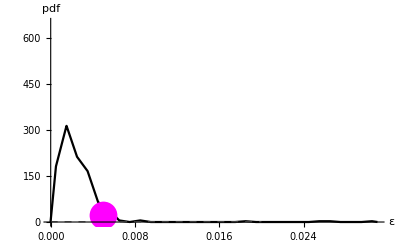
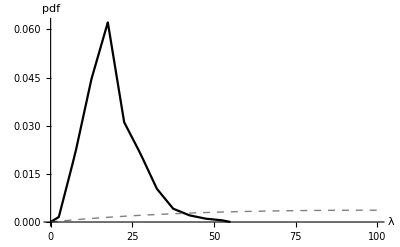
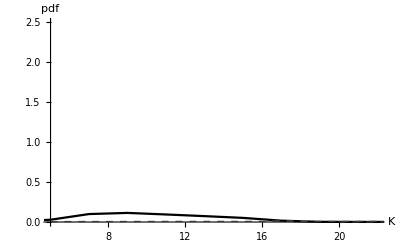

```mathematica
tick1={Automatic,Automatic};
tick2={Automatic,Automatic};
tick3=tick4={Automatic,Automatic};
ticks={tick1,tick2,tick3,tick4};
gh1=listmcplot[reshyper,truehyper,hyperlab,withdata]
(*gh2=listhisplot[reshyper,truehyper,hyperlab,withdata,ticks,PlotRangePadding->None,AxesStyle->Thickness[linethick],TicksStyle->Thickness[linethick]]; *)
gh2=Table[PosteriorPDFPlot[reshyper[[All,i]],1,PlotRange->All,PlotRangePadding->None,Ticks->ticks[[i]],PlotStyle->plotstyle,AxesLabel->{hyperlab[[i]],"pdf"}],{i,Length[hyperlab]}];
If[modelid=="LD",
ls=SortBy[Tally[reshyper[[All,4]] ],First];
ls[[All,2]]=ls[[All,2]]/(Total[ls[[All,2]]] Mean[Differences[ls[[All,1]]]]);
ls=Join[{{ls[[1,1]],0}},ls,{{20,0}}];
gh2[[-1]]=ListLinePlot[ls,PlotStyle->plotstyle]
];
pri2=Plot[PDF[epsdist,x],{x,0,0.02},PlotRange->All,PlotStyle->{Gray,Dashed,Thick}];
pri1=Plot[PDF[thetadist,x],{x,prithetamin,100},PlotRange->All,PlotStyle->{Gray,Dashed,Thick }];
pri3=Plot[PDF[rhodist,x],{x,0,If[modelid=="LD",1000,100]},PlotRange->All,PlotStyle->{Gray,Dashed,Thick}];
(*pri4=PosteriorPDFPlot[Select[prires[[All,1]],#≥5&],1,PlotRange->All,PlotStyle->{Gray,Dashed,Thick}];*)
ls=SortBy[Tally[prires[[All,1]]],First];
ls[[All,2]]/=Total[ls[[All,2]]];
ls=Select[ls,#[[1]]≥5&];
ls=Join[ls,{{20,0}}];
pri4=ListLinePlot[ls,PlotRange->All,PlotStyle->{Gray,Dashed,Thick}];
ls=SortBy[Tally[prires[[All,1]]],First];
ls[[All,2]]/=Total[ls[[All,2]]];
ls=Select[ls,#[[1]]≥5&];
ls=Join[ls,{{20,0}}];
pri4=ListLinePlot[ls,PlotRange->All,PlotStyle->{Gray,Dashed,Thick}];
gh3=Show[#,PlotRange->All,AxesOrigin->{0,0}]&/@Transpose[{gh2,{pri1,pri2,pri3,pri4}}];
gh3[[1]]=Show[gh3[[1]],PlotRange->{{0,100},All}];
gh3[[2]]=Show[gh3[[2]],PlotRange->{All,{0,650}},Epilog->{PointSize[0.05],Magenta,Point[{truehyper[[2]],24}]}];
(*gh3[[4]]=Show[gh3[[4]],PlotRange->{{5,25},{0,2.5}},AxesOrigin->{5,0},Epilog->{PointSize[0.05],Magenta,Point[{truehyper[[4]],0.1}]}];*)
gh3[[4]]=Show[gh3[[4]],PlotRange->{{5,22},{0,2.5}},AxesOrigin->{5,0}];
gh3
```

```mathematica
(*****************************************************************************************************************)
```

{0.0312,Null}

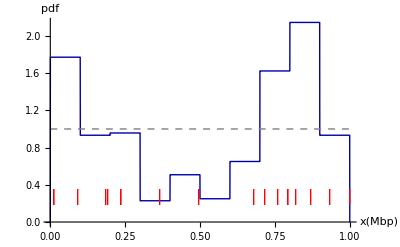

```mathematica
rescpls=Flatten[Table[
ls=SplitBy[rescold[[k,4]],#[[2]]&];
ls=ls[[All,1]];
Rest[ls[[All,1]]],{k,Length[rescold]}]/10^6.];//Timing
gcp=Show[PosteriorPDFPlot[rescpls,0,PlotRange->All,PlotStyle->Darker[Blue]],Plot[PDF[UniformDistribution[{0,nbp/10^6}],x],{x,0,nbp/10^6},PlotStyle->{Gray, Thick,Dashed}],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"x(Mbp)","pdf"}];
If[withdata,
SeedRandom[100];
gcp=Show[gcp,ListPlot[Thread[{Rest[trueibdloc/10^6.],0.27}],PlotMarkers->{"|",16},PlotStyle->Red,PlotRange->All]];
SeedRandom[]
];
gcp
```

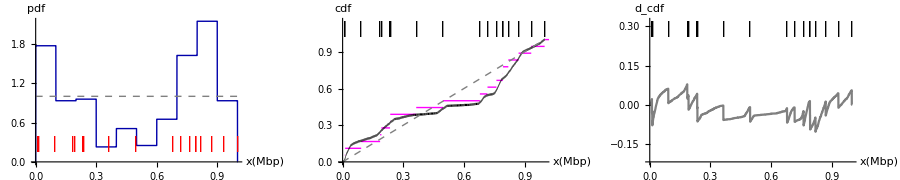

```mathematica
dist1=EmpiricalDistribution[Rest[trueibdloc/10^6]];
g1=DiscretePlot[CDF[dist1,x],{x,DistributionDomain[dist1]},ExtentSize->Right,Filling->None,PlotStyle->Directive[Magenta,Thick]];
dist2=EmpiricalDistribution[rescpls];
g2=DiscretePlot[CDF[dist2,x],{x,DistributionDomain[dist2]},ExtentSize->Right,Filling->None,PlotStyle->Directive[Black,Thickness[linethick]]];
g3=Plot[x 10^6/nbp,{x,0,nbp/10^6},PlotStyle->{Gray,Thick,Dashed}];
gcp2=Show[g1,g2,g3,PlotRange->{{0,nbp/10^6},{0,1.15}},AxesOrigin->{0,0},AxesLabel->{"x(Mbp)","cdf"},PlotRangePadding->None];
If[withdata,
gcp2=Show[gcp2,ListPlot[Thread[{Rest[trueibdloc/10^6.],1.09}],PlotMarkers->{"|",16},PlotStyle->Directive[Black,Thickness[linethick]],PlotRange->All]];
gcp3=Plot[CDF[dist2,x]-CDF[dist1,x],{x,0,nbp/10^6},AxesOrigin->{0,-0.22},PlotRange->{{0,nbp/10^6},{-0.22,0.32}},PlotStyle->{If[StringCount[datafile,"-LD"]==1,Black,Gray],Thickness[linethick]},AxesLabel->{"x(Mbp)","d_cdf"}];
gcp3=Show[gcp3,ListPlot[Thread[{Rest[trueibdloc/10^6.],0.29}],PlotMarkers->{"|",16},PlotStyle->{Black,Thickness[linethick]},PlotRange->All]]
];
GraphicsRow[{gcp,gcp2,gcp3},ImageSize->900]
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
getsnptbl[yls_,xls_]:=Module[{yls2,map},
yls2=If[yls[[-1,1]]==nbp,yls,Append[yls,{nbp,yls[[-1,2]]}]];
map=IndexByInterpolation[yls2[[All,1]]];
yls2[[map[xls],2]]
]
```

```mathematica
resibd=rescold[[All,4,All,;;2]];
pos=ysnp[[All,1]];
ressnpibd=Transpose[getsnptbl[#,pos]&/@resibd];//Timing
truesnpibd=getsnptbl[Transpose[{trueibdloc,trueibd}],pos];
```

{0.39,Null}

```mathematica
(*****************************************************************************************************************)
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
If[1==1,
ibddis=Table[
ls=(IBDTransitionType2[{#,truesnpibd[[i]]}]&/@ressnpibd[[i]])[[All,1]];
ls2=Tally[ls];
ls2[[All,2]]/=N[Length[ls]];
ls2[[All,1]]=(ls2[[All,1]]/.{-1->3})+1;
ls=Table[0,{4}];
ls[[ls2[[All,1]]]]=ls2[[All,2]];
ls,{i,Length[ressnpibd]}];
ibddis=Transpose[Accumulate[Transpose[ibddis]]];
(*Export["ibddis"<>dataid<>".txt",ibddis,"Table"],
ibddis=Import["ibddis"<>dataid<>".txt","Table"];*)
];//Timing
```

{5.56924,Null}

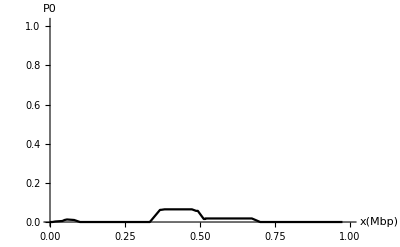
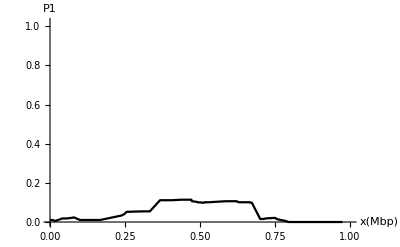
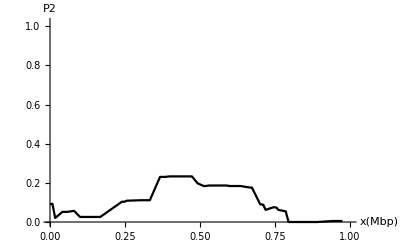

```mathematica
figp=Table[ListPlot[Transpose[{ysnp[[All,1]]/10^6.,ibddis[[All,i]]}],PlotStyle->plotstyle,Joined->True,PlotRange->{{0,nbp/10^6},{0,1.02}},AxesLabel->{"x(Mbp)","P"<>ToString[i-1]}],{i,3}]
```

```mathematica
ls=Table[Transpose[{ysnp[[All,1]]/10^6.,ibddis[[All,i]]}],{i,3}];
ls2=Select[ls[[1]],0.35≤First[#]≤0.7&];
Quantile[ls2[[All,2]],{0,0.5,0.975}]
Mean[ls2[[All,2]]]
```

{0.015544,0.0181347,0.0647668}

0.0369603

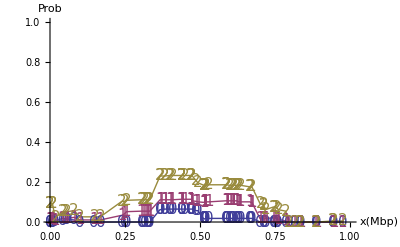

```mathematica
colorg1=ListPlot[Table[Transpose[{ysnp[[All,1]]/10^6.,ibddis[[All,i]]}],{i,3}],Joined->True,PlotRange->{{0,nbp/10^6},{0,1}},PlotMarkers->{{"0",15},{"1",15},{"2",15}},AxesLabel->{"x(Mbp)","Prob"}]
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
figs=Join[gh3,{gcp,gcp2,gcp3},figp];
```

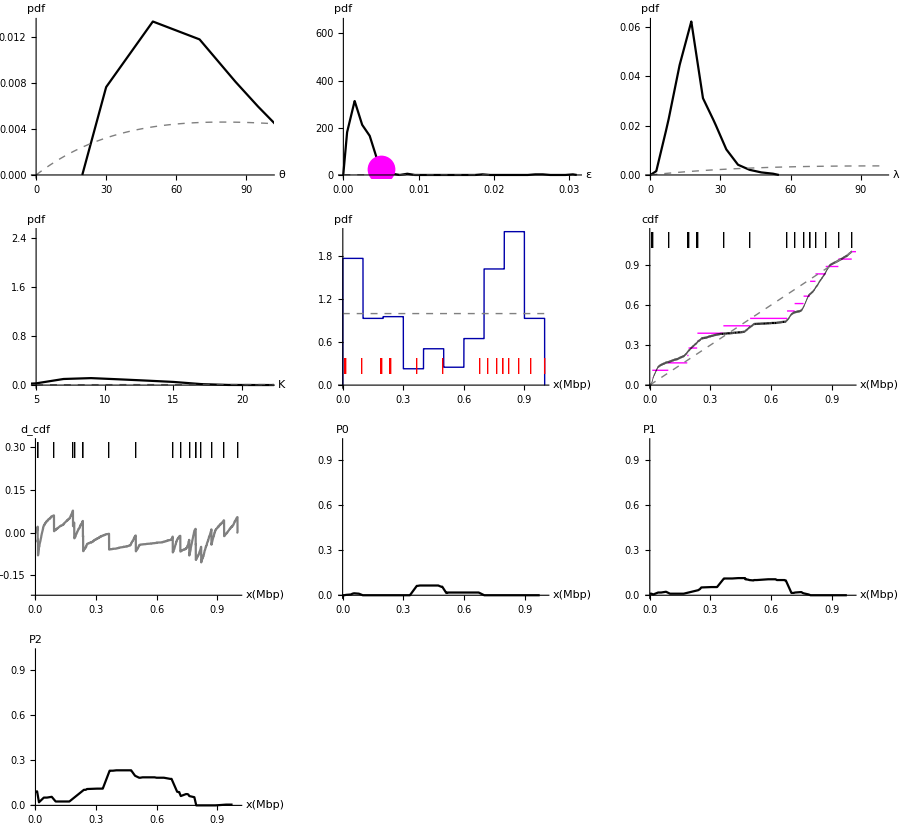

```mathematica
outg=GraphicsGrid[Partition[Join[figs,{Null,Null}],3],ImageSize->900]
(*Export["figs_"<>dataid<>".pdf",outg]*)
```

```mathematica
(*****************************************************************************************************************)
```

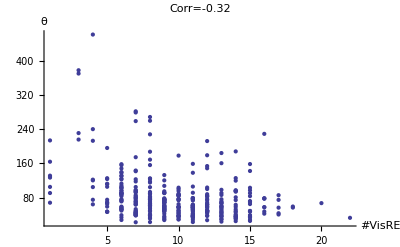
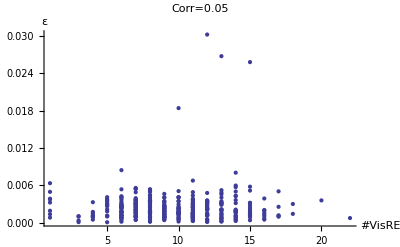
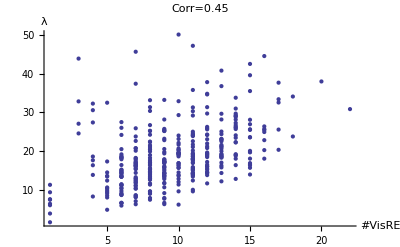

```mathematica
gcorre=Table[
ls=Table[Count[Equal@@#&/@Partition[rescold[[k,4,All,2]],2,1],False],{k,Length[rescold]}];
ls=Transpose[{ls,reshyper[[All,i]]}];
Show[
ListPlot[ls,AxesOrigin->{0,0},PlotRange->All,PlotLabel->Style["Corr="<>ToString[Round[Correlation[ls[[All,1]],ls[[All,2]]],0.01]],20],AxesLabel->{"#VisRE",hyperlab[[i]]}]
],{i,3}]
```

```mathematica
i=3;
ls=Table[Count[Equal@@#&/@Partition[rescold[[k,4,All,2]],2,1],False],{k,Length[rescold]}];
ls=Transpose[{ls,reshyper[[All,i]]}];
gcorcp=Show[
ListPlot[ls,AxesOrigin->{0,0},PlotRange->All,PlotLabel->Style["Corr="<>ToString[Round[Correlation[ls[[All,1]],ls[[All,2]]],0.01]],20],AxesLabel->{"#VisRE",hyperlab[[i]]}]
];
If[withdata,gcorcp=Show[gcorcp,ListPlot[{{Count[Equal@@#&/@Partition[trueibd,2,1],False],truehyper[[i]]}},PlotStyle->Red,PlotMarkers->{Automatic,20}]]
];
gcorcp
```

-Graphics-

{θ,ε,λ,K}

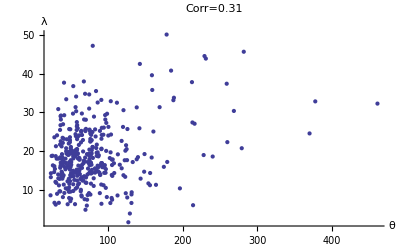
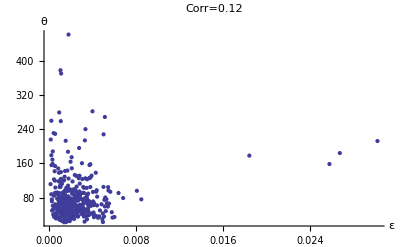
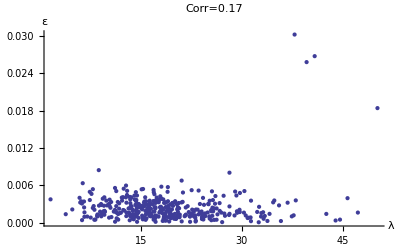

```mathematica
hyperlab
ijls={{1,3},{2,1},{3,2}};
gcorhyper=Table[
{i,j}=ij;
ls=reshyper[[All,{i,j}]];
gg=Show[
ListPlot[ls,AxesOrigin->{0,0},PlotRange->All,PlotLabel->Style["Corr="<>ToString[Round[Correlation[ls[[All,1]],ls[[All,2]]],0.01]],20],AxesLabel->{hyperlab[[i]],hyperlab[[j]]}]
];
If[withdata,gg=Show[gg,ListPlot[{truehyper[[{i,j}]]},PlotStyle->Red,PlotMarkers->{Automatic,20}]]
];
gg,{ij,ijls}]
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
(*****************************************************************************************************************)
```

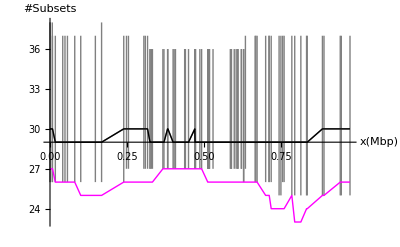

```mathematica
ls=Transpose[Map[Length,ressnpibd,{2}]];
q=Quantile[ls,{0.025,0.5,0.975}];
errls=Table[{{ysnp[[i,1]]/10^6.,q[[i,2]]},ErrorBar[q[[i,{1,3}]]-q[[i,2]]]},{i,Length[q]}];
gnsub=ErrorListPlot[errls,AxesLabel->{"x(Mbp)","#Subsets"},Joined->True,PlotStyle->Gray,PlotRange->All,PlotRangePadding->None];
gnsub=Show[gnsub,ListLinePlot[errls[[All,1]],PlotStyle->{Black,Thick}]];
If[withdata,
gnsub=Show[gnsub,
ListPlot[Transpose[{ysnp[[All,1]]/10^6.,Length[#]&/@truesnpibd}],PlotStyle->{Magenta,Thick},Joined->True]
]
];
gnsub
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
IBDSimilarity3[z1_,z2_]:=Module[{n,m1,m2,ls,res},
m1=m2=IdentityMatrix[Max[z1]];
Scan[(m1[[#,#]]=1)&,DeleteCases[z1,{_}],{1}];
Scan[(m2[[#,#]]=1)&,DeleteCases[z2,{_}],{1}];
m1=ReplacePart[m1,{i_,i_}->-10];
m2=ReplacePart[m2,{i_,i_}->-10];
ls=Rest[Tally[Transpose[{Flatten[m1],Flatten[m2]}]]];
ls[[All,1]]+=1;
res=ConstantArray[0,{2,2}];
Scan[(res[[#[[1,1]],#[[1,2]]]]=#[[2]])&,ls];
res
]
```

```mathematica
ibddis3=Transpose[Table[IBDSimilarity3[truesnpibd[[i]],#]&/@ressnpibd[[i]],{i,Length[ressnpibd]}]];//Timing
```

{42.68187,Null}

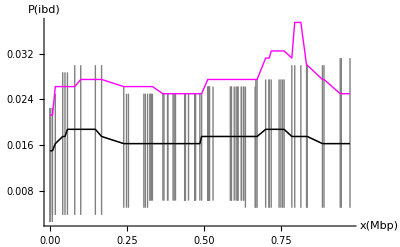

```mathematica
ls=(ibddis3[[All,All,1,2]]+ibddis3[[All,All,2,2]])/nsq^2.;
q=Quantile[ls,{0.025,0.5,0.975}];
errls=Table[{{ysnp[[i,1]]/10^6.,q[[i,2]]},ErrorBar[q[[i,{1,3}]]-q[[i,2]]]},{i,Length[q]}];
ls2=(IBDSimilarity3[#,#]&/@truesnpibd)/nsq^2;
figibd=ErrorListPlot[errls,AxesLabel->{"x(Mbp)","P(ibd)"},Joined->True,PlotStyle->Gray,PlotRange->All,PlotRangePadding->None,AxesOrigin->{0,0}];
figibd=Show[figibd,ListLinePlot[errls[[All,1]],PlotStyle->{Black,Thick},PlotRange->All]];
If[withdata,
figibd=Show[
figibd,
ListPlot[Transpose[{ysnp[[All,1]]/10^6.,ls2[[All,2,2]]}],PlotStyle->{Magenta,Thick},Joined->True,PlotRange->All]
]
];
figibd
```

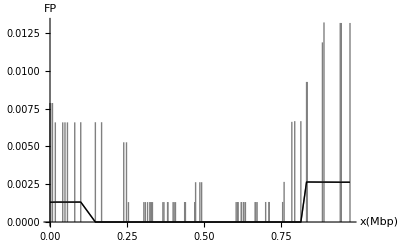

```mathematica
ls=ibddis3[[All,All,1,2]]/(ibddis3[[All,All,1,2]]+ibddis3[[All,All,1,1]]);
q=Quantile[ls,{0.025,0.5,0.975}];
errls=Table[{{ysnp[[i,1]]/10^6.,q[[i,2]]},ErrorBar[q[[i,{1,3}]]-q[[i,2]]]},{i,Length[q]}];
figfp=ErrorListPlot[errls,AxesLabel->{"x(Mbp)","FP"},Joined->True,PlotStyle->Gray,PlotRange->All,PlotRangePadding->None,AxesOrigin->{0,0}];
figfp=Show[figfp,ListLinePlot[errls[[All,1]],PlotStyle->{Black,Thick},PlotRange->All]]
```

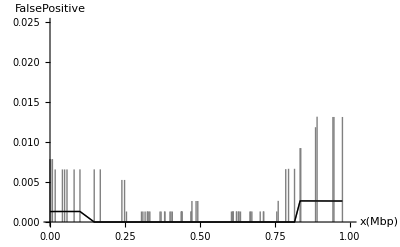

```mathematica
gfpibd=Show[figfp,LabelStyle->Directive[FontSize->16,FontFamily->"Times"],PlotRange->{{0,1},{0,0.025}},AxesLabel->{"x(Mbp)","FalsePositive"}]
```

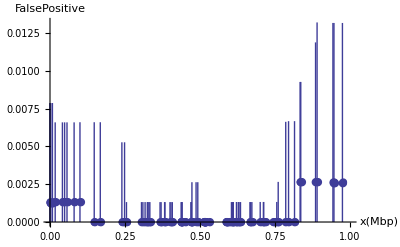

```mathematica
ls=ibddis3[[All,All,1,2]]/(ibddis3[[All,All,1,2]]+ibddis3[[All,All,1,1]]);
q=Quantile[ls,{0.025,0.5,0.975}];
errls=Table[{{ysnp[[i,1]]/10^6.,q[[i,2]]},ErrorBar[q[[i,{1,3}]]-q[[i,2]]]},{i,Length[q]}];
figfp2=ErrorListPlot[errls,AxesLabel->{"x(Mbp)","FalsePositive"},PlotMarkers->{Automatic,0},PlotRange->{{0,1},All},PlotRangePadding->None,AxesOrigin->{0,0}];
colorg2=Show[figfp2,ListPlot[errls[[All,1]],PlotMarkers->{Automatic,10}],LabelStyle->Directive[FontSize->16,FontFamily->"Times"]]
```

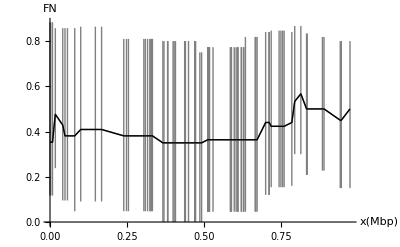

```mathematica
ls=ibddis3[[All,All,2,1]]/(ibddis3[[All,All,2,1]]+ibddis3[[All,All,2,2]]);
q=Quantile[ls,{0.025,0.5,0.975}];
errls=Table[{{ysnp[[i,1]]/10^6.,q[[i,2]]},ErrorBar[q[[i,{1,3}]]-q[[i,2]]]},{i,Length[q]}];
figfn=ErrorListPlot[errls,AxesLabel->{"x(Mbp)","FN"},Joined->True,PlotStyle->Gray,PlotRange->All,PlotRangePadding->None,AxesOrigin->{0,0}];
figfn=Show[figfn,ListLinePlot[errls[[All,1]],PlotStyle->{Black,Thick},PlotRange->All]]
```

```mathematica
(*****************************************************************************************************************)
```

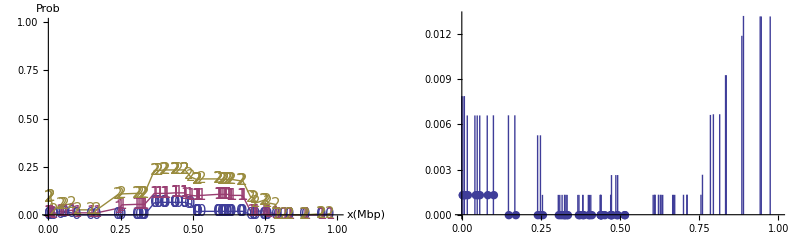

```mathematica
GraphicsRow[{colorg1,colorg2},ImageSize->800]
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
gg=Join[{gnsub,figibd,figfp,figfn},gcorre,gcorhyper];
```

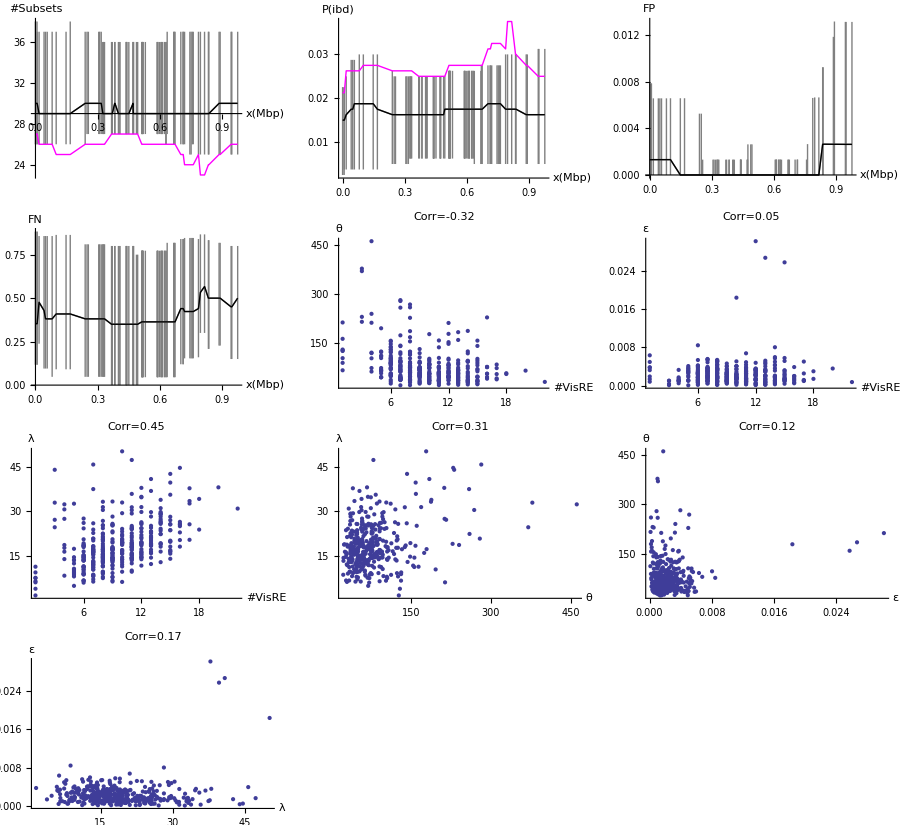

```mathematica
outg2=GraphicsGrid[Partition[Join[gg,{Null,Null}],3],ImageSize->900]
(*Export["gg_"<>dataid<>".pdf",outg2]*)
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
(*****************************************************************************************************************)
```